```mathematica
<<Vilcretas`
```

VilCretas está disponible.

```mathematica
<<TutoriasED`
```

Se ha cargado el paquete TutoriasED. USO PARA ESTUDIO. Versión 23/03/2025

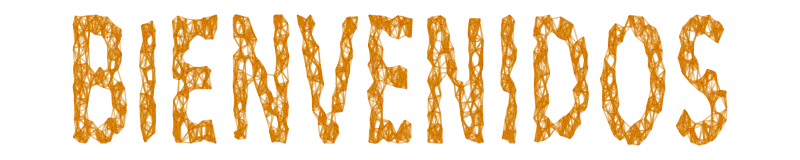

```mathematica
GrafoString["BIENVENIDOS"]
```

```mathematica
A = {100,8,55,34,81,1,39,87,53,16};
B= {13,62,21,66,44,88,93,95,80,16};
H = {22,64,5,18,95,72,52,44,98,10};
R1 = {{8,88},{100,80},{53,80},{100,44},{87,93},{53,16},{8,93},{87,13},{1,62},{100,93}};
R2 = {{16,22},{95,98},{88,10},{66,5},{80,72},{21,22},{88,44},{62,72},{80,22},{66,72}};
(*RelacionComposicion[R2,R1]*)
MR1 =MatrizRelBin[R1,A,B][[1]];
MR2 =MatrizRelBin[R2,B,H][[1]];
MR = RelBinMatriz[ProductoBooleano[MR1,MR2,lista->True],A,H]
```

{{1,72},{8,10},{8,44},{53,22},{53,72},{100,22},{100,72}}

```mathematica
respuestas = {{100,22},{87,95},{1,72},{39,64},{53,22},{34,10}};
```

```mathematica
relacion = {{1,72},{8,10},{8,44},{53,22},{53,72},{100,22},{100,72}};
```

```mathematica
existeElementoRelBin[relacion, respuestas]
```

Tabla de Elementos y su Relación Binaria:

Elemento | Relación Binaria
{100,22} | True
{87,95} | False
{1,72} | True
{39,64} | False
{53,22} | True
{34,10} | False

```mathematica
Table[i->ElementRelBinQ[relacion,i],{i, respuestas}]
```

{{100,22}→True,{87,95}→False,{1,72}→True,{39,64}→False,{53,22}→True,{34,10}→False}

```mathematica
Clear[A,R1,R2]
```

```mathematica
A={29,58,59,11,22,47};
R1={{58,58},{29,59},{22,47},{47,22},{11,58},{11,47},{59,47},{22,59},{58,11},{22,58}};
R2={{58,58},{29,59},{59,59},{58,47},{11,11},{11,47},{22,11},{11,59},{59,11},{47,47}};
```

```mathematica
Clear[MR1,MR2]
```

```mathematica
MR1=MatrizRelBin[R1,A,A][[1]];
MR2=MatrizRelBin[R2,A,A][[1]]
```

{{0,0,1,0,0,0},{0,1,0,0,0,1},{0,0,1,1,0,0},{0,0,1,1,0,1},{0,0,0,1,0,0},{0,0,0,0,0,1}}

```mathematica
Clear[MR]
```

```mathematica
MR=UnionBooleana[UnionBooleana[ComplementoBooleano[MR1][[1]], MR2][[1]], Transpose[InterseccionBooleana[MR2, Transpose[MR1]][[1]]]]
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0 | 1)

```mathematica
A={9,106,132,18,28,44,72,61,94,2};

R={{2,2},{2,18},{2,94},{9,9},{9,106},{18,2},{18,18},{18,94},{28,28},{44,44},{44,61},{61,44},{61,61},{72,72},{94,2},{94,18},{94,94},{106,9},{106,106},{132,132}};
```

```mathematica
-Graphics--Graphics-
```

```mathematica
ClasesEquivalencia[R,A]
```

[9]={9,106}

[106]={9,106}

[132]={132}

[18]={18,94,2}

[28]={28}

[44]={44,61}

[72]={72}

[61]={44,61}

[94]={18,94,2}

[2]={18,94,2}

El conjunto de clases de equivalencia distintas es:

{{9,106},{132},{18,94,2},{28},{44,61},{72}}

```mathematica
A={46,31,40,66,30,37};
R={{46,46},{46,40},{31,46},{31,37},{31,30},{40,40},{40,30},{66,40},{66,46},{66,30},{30,37},{30,66},{30,46},{37,37},{37,31}};
```

```mathematica
MatrizRelBin[R,A,A]
```

```mathematica
({{1, 0, 1, 0, 0, 0}, {1, 0, 0, 0, 1, 1}, {0, 0, 1, 0, 1, 0}, {1, 0, 1, 0, 1, 0}, {1, 0, 0, 1, 0, 1}, {0, 1, 0, 0, 0, 1}})-Graphics-
```

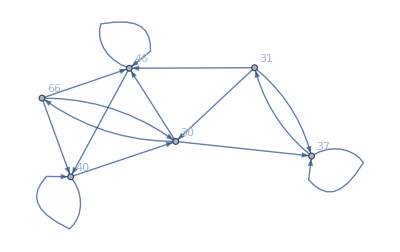

```mathematica
GrafoRelBin[R,A]
```

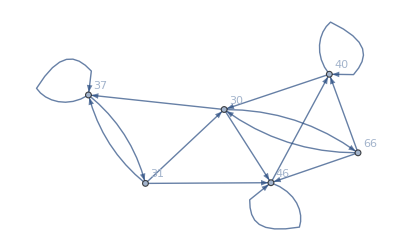

```mathematica
Grafo[R,dirigido->True]
```

```mathematica
A=Range[-30,996,18];
B=Range[-30,998,4];
```

```mathematica
Length[PC[A,B]]
```

14964

```mathematica
RelacionComposicion[R1_,R2_]:=Module[{Composicion={},i,j},For[i=1,i≤Length[R2],For[j=1,j≤Length[R1],If[R2[[i,2]]==R1[[j,1]],Composicion=Append[Composicion,{R2[[i,1]],R1[[j,2]]}]];j++];
i++];DeleteDuplicates[Composicion]]
```

```mathematica
A={100,8,55,34,81,1,39,87,53,16};

B={13,62,21,66,44,88,93,95,80,16};

H={22,64,5,18,95,72,52,44,98,10};

R1={{8,88},{100,80},{53,80},{100,44},{87,93},{53,16},{8,93},{87,13},{1,62},{100,93}};

R2={{16,22},{95,98},{88,10},{66,5},{80,72},{21,22},{88,44},{62,72},{80,22},{66,72}};
```

```mathematica
relaciones = RelacionComposicion[R2,R1]
```

{{8,10},{8,44},{100,72},{100,22},{53,72},{53,22},{1,72}}

```mathematica
respuestas={{100,22},{34,10},{53,22},{39,64},{87,95},{1,72}};
```

```mathematica
existeElementoRelBin[relaciones, respuestas]
```

Tabla de Elementos y su Relación Binaria:

Elemento | Relación Binaria
{100,22} | True
{34,10} | False
{53,22} | True
{39,64} | False
{87,95} | False
{1,72} | True

```mathematica
A=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Clear[A,R]
```

```mathematica
R = RelBin["a^3-b^3>=96&&Mod[a+b,11]==0", A,A]
```

{{7,4},{8,3},{9,2},{10,1},{12,10},{13,9},{14,8},{15,7},{16,6},{17,5},{17,16},{18,4},{18,15},{19,3},{19,14},{20,2},{20,13}}

```mathematica
Length[DominioRelBin[R]]
```

13